```mathematica
(*F, IOF: input-output function*)
```

```mathematica
ce=310;eIth=125;ge=.16;tre=2;gi=.087;tri=1;ti=5;te=100;ci=615;Io=.3 (*background noise*);iIth=177;Is=.26(*stimulus*);a=64/100;
```

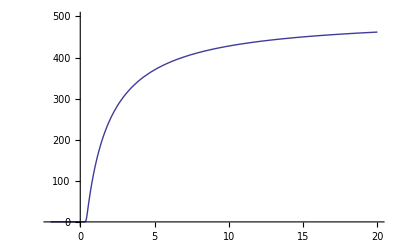

```mathematica
(*excitatory F*) Plot[(ce I-eIth)/(1- Exp[-ge(ce I-eIth)]+tre/1000(ce I-eIth) ),{I,-2,20},PlotRange->{0,500}]
```

```mathematica
Clear[ce,eIth,tre,ge,ci,iIth,tri,gi]
```

```mathematica
D[(ce l-eIth)/(1- Exp[-ge(ce l-eIth)]+tre/1000(ce l-eIth) ),l]
```

-((31/50+49.6 ⅇ^(-0.16 (-125+310 l))) (-125+310 l))/((1-ⅇ^(-0.16 (-125+310 l))+1/500 (-125+310 l))^2)+310/(1-ⅇ^(-0.16 (-125+310 l))+1/500 (-125+310 l))

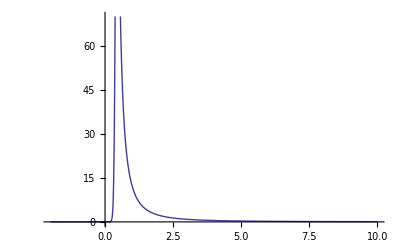

```mathematica
Plot[-((-eIth+ce l) (ce ⅇ^(-ge (-eIth+ce l)) ge+(11 ce tre)/1000))/((1-ⅇ^(-ge (-eIth+ce l))+(11 (-eIth+ce l) tre)/1000)^2)+ce/(1-ⅇ^(-ge (-eIth+ce l))+(11 (-eIth+ce l) tre)/1000),{l,-2,10}, PlotRange->{0,70}]
```

```mathematica
(*excitatory F: slope=67 middle section*)
```

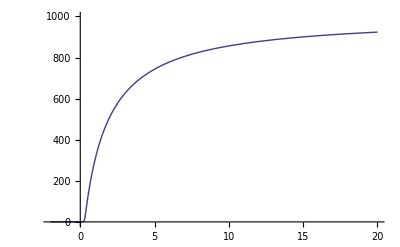

```mathematica
(*inhibitory F*) Plot[(ci I-iIth)/(1- Exp[-gi(ci I-iIth)]+tri/1000(ci I-iIth)),{I,-2,20},PlotRange->{0,1000}]
```

```mathematica
((*excitatory F: slope=150 middle section*))
```

```mathematica
(*change Jee largely changes Se nullcline only!*)
```

```mathematica
(*which section corresponds to which part of Si_Se phase plane, then find best approxiamtion of F slope in the middle section of Si_Se. The intersection in Si_Se plane can only happen within the middle section! just look at the function behaviors for dSe/dt=0*)
```

```mathematica
Jee=.5;Jie=.5;Si=.5;
```

```mathematica
(*S1, should keep it low in order to use middle section slope*)(eIth/ce+Jie Si -Is-Io)/Jee
```

0.186452

```mathematica
(*S2*)( 6- Jie Si -Is)/Jee
```

10.98

```mathematica
N[iIth/ci]
```

0.287805

```mathematica
Clear[te]
```

```mathematica
(*Si in terms of Se (dSi/dt=0), middle section*)
```

```mathematica
Si=k2(c4 +c5(Se-S1))/(1/ti+k2 c6 );
```

```mathematica
(*Solve for Se in linearized system, middle section*)
```

```mathematica
Simplify[Solve[ -(Se-S1)/te+k1(1-Se+S1)(c1+c2(Se-S1)-c3 Si  )==0,Se]]
```

{{Se→(-1-5 c6 k2-c1 k1 te+c2 k1 te+5 c3 c4 k1 k2 te-5 c3 c5 k1 k2 te-5 c1 c6 k1 k2 te+5 c2 c6 k1 k2 te+2 c2 k1 S1 te-10 c3 c5 k1 k2 S1 te+10 c2 c6 k1 k2 S1 te+√((1+c1 k1 te-c2 k1 te-5 c3 c4 k1 k2 te+5 c3 c5 k1 k2 te-2 c2 k1 S1 te+10 c3 c5 k1 k2 S1 te+5 c6 k2 (1+c1 k1 te-c2 k1 (1+2 S1) te))^2+4 k1 (c2-5 c3 c5 k2+5 c2 c6 k2) te (k1 (c1-5 c3 c4 k2+5 c1 c6 k2) te-k1 (c2-5 c3 c5 k2+5 c2 c6 k2) S1^2 te+S1 (1+c1 k1 te-c2 k1 te-5 c3 c4 k1 k2 te+5 c3 c5 k1 k2 te+5 c6 k2 (1+c1 k1 te-c2 k1 te)))))/(2 k1 (c2-5 c3 c5 k2+5 c2 c6 k2) te)},{Se→-(1+5 c6 k2+c1 k1 te-c2 k1 te-5 c3 c4 k1 k2 te+5 c3 c5 k1 k2 te+5 c1 c6 k1 k2 te-5 c2 c6 k1 k2 te-2 c2 k1 S1 te+10 c3 c5 k1 k2 S1 te-10 c2 c6 k1 k2 S1 te+√((1+c1 k1 te-c2 k1 te-5 c3 c4 k1 k2 te+5 c3 c5 k1 k2 te-2 c2 k1 S1 te+10 c3 c5 k1 k2 S1 te+5 c6 k2 (1+c1 k1 te-c2 k1 (1+2 S1) te))^2+4 k1 (c2-5 c3 c5 k2+5 c2 c6 k2) te (k1 (c1-5 c3 c4 k2+5 c1 c6 k2) te-k1 (c2-5 c3 c5 k2+5 c2 c6 k2) S1^2 te+S1 (1+c1 k1 te-c2 k1 te-5 c3 c4 k1 k2 te+5 c3 c5 k1 k2 te+5 c6 k2 (1+c1 k1 te-c2 k1 te)))))/(2 k1 (c2-5 c3 c5 k2+5 c2 c6 k2) te)}}